```mathematica
(* Calculate thermistor curve and resistor values for op amp schmitt trigger temperature controller
Electric Sheep Labs
11-5-2017
Notes:
1. Take resistor readings of the thermistor at room temp, freezing, and boiling
  2. Fill in the values in the array below (first entry in the NonlinearMidelFit function)
  3. pass upper and lower temp values to the thermistorCurve function to find the upper and lower resistances
  4. Pick fixed resistor to make divider with the thermistor and see what the voltages will be
  5. Pick voltage rail value and then play with resistances of the op amp schmitt trigger to get same vHigh and vLow as the thermistor divider... the method to do this is poorly described in this section. :D 
**NOTE: all resistances are in kOhms unless otherwise noted...
*)

thermistorCurve = NonlinearModelFit[{{0,32.800},{20.56,12.050},{100,.670}},a+b Exp[-x/c],{{a,0},{b,30},{c,20}},x]
```

FittedModel[0.449441+32.3506 ⅇ^(-0.0498822 x)]

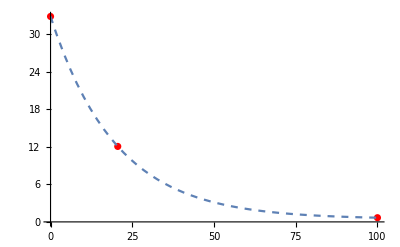

```mathematica
Show[ListPlot[{{0,32.800},{20.56,12.050},{100,.670}}, PlotStyle->Red, PlotRange->All],Plot[thermistorCurve[x],{x,0,100}, PlotStyle->Dashed, PlotRange->All]]
```

```mathematica
(*2.77C is 37F, 8.33C is 47F, so find the resistances at those temps by plugging into the thermistor curve*)
```

```mathematica
RlowTemp = thermistorCurve[2.777]
```

28.6152

```mathematica
RhighTemp = thermistorCurve[8.333]
```

21.7975

```mathematica
(*pick a resistor with which to make a voltage divider with the thermistor, I picked something pretty close to the value of the thermistor around the temp range I was using.
Below is the simple voltage divider equation to see what the output voltages will be at the limits of our temperature range, and an image depicting the divider with the thermistor (R1 is Rfixed). *)
```

```mathematica
Rfixed = 25;
```

```mathematica
VlowTemp = RlowTemp/(Rfixed+RlowTemp)*5.8
```

3.09555

```mathematica
VhighTemp = RhighTemp/(Rfixed+RhighTemp)*5.8
```

2.70155

```mathematica
(*Above are the voltage values we will get when the thermistor is at the min and max readings we want, so now we calculate the upper and lower voltage thresholds for the schmitt trigger so that they match these. I recommend first setting V (below) to the supply rail, then set rfb to get the absolute difference of the 
voltages (abs(Vhigh-Vlow)) to about the same as the voltage difference as the above values. Then play with r2 to bring up the lower voltage to the exact value...*)
```

```mathematica
V = 5.8;
r1 = 1;
r2  =1;
rfb = 7;

tripPointWhenOff= V*(1/r2+1/rfb)^(-1)/((1/r2+1/rfb)^(-1)+r1)//N
tripPointWhenOn= V*r2/(r2+(1/r1+1/rfb)^(-1))//N
```

2.70667

3.09333

```mathematica
(*The above calculations are just voltage divider equations to find the upper and lower thresholds of the Schmitt Trigger. The schematic above can be simplified to a simple voltage divider when the output is either high or low, and the voltage divider configuration becomes apparent (see below). When the output of the op amp is "high" (below left), Rfb is tied to the voltage rail and is in parallel with R1, and thus tripPointWhenOn is the divider equation utilized. 
When the op amp is "low" (below left), Rfb is pulled to ground and is in parallel with R2, and tripPointWhenOff is the divider 
equation used to calculate the new reference voltage.*)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
(*Final Comments:
The inspiration for this script was to explain how I made my temperature controller for my keezer (beer fridge from a chest freezer). The remaining unaddressed details are as follows: - I used a simple solid-state relay (SSR, from Amazon's finest selection of relays) in series with the mains to the freezer to turn it on and off. The relay should of course be able to handle the current draw of the compressor in your freezer,      and also be able to be switched by the output of your Schmitt trigger circuit. 
- To get logic level power, I tore apart an old phone charger that output 5.8 volts jankly soldered it onto the same mains cable as the compressor*)
```